```mathematica
(*Лабораторная работа №4*)
(*По курсу «Защита информационных процессов в компьютерных системах»*)
(*Встраивание видимого ЦВЗ в пространственной области*)

(*
	Кутузов Илья
	А-12м-20
*)
nnom=10;

(*Задание 3*)
(*3. Импортировать файл box.bmp в пакет "Mathematica" (Import[]) и определить размеры рисунка-ImageDimensions[].*)
box=Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\box.bmp"]
ImageDimensions[box]
```

-Graphics-

{220,30}

```mathematica
(*Задание 4*)
(*4. Вывести первую и последнюю строку изображения в формате RGB-данных с помощью функции ImageData[***,"Byte"]*)
data=ImageData[box,"Byte"];
data[[1,All,All]]
data[[30,All,All]]
```

{{35,69,79},{25,59,69},{20,58,59},{21,56,58},{14,48,49},{1,32,34},{23,53,53},{27,55,56},{43,69,68},{16,42,41},{25,53,56},{54,82,85},{16,44,47},{17,45,48},{36,64,67},{44,72,75},{23,51,54},{15,43,44},{31,60,58},{24,52,55},{22,51,59},{24,54,65},{66,100,112},{51,87,99},{46,84,93},{54,91,99},{30,61,66},{18,48,59},{53,84,102},{58,92,117},{59,94,122},{49,89,115},{24,66,91},{10,51,81},{57,102,143},{104,151,193},{66,114,162},{54,104,155},{74,124,177},{73,120,176},{103,148,203},{89,132,187},{80,125,182},{90,135,192},{88,133,192},{86,130,191},{88,132,195},{72,116,181},{63,106,174},{95,138,206},{90,131,197},{83,123,192},{92,132,201},{87,127,197},{88,128,198},{88,128,200},{88,128,200},{88,128,200},{89,132,201},{90,133,202},{88,131,200},{85,128,197},{86,129,198},{86,129,198},{86,129,198},{86,129,198},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{86,129,198},{85,128,197},{84,127,196},{83,126,195},{83,126,195},{83,126,195},{83,126,195},{83,126,195},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,128,197},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{86,130,201},{84,128,199},{82,126,197},{81,125,196},{83,127,198},{83,127,198},{83,127,198},{83,127,198},{85,127,199},{85,127,199},{85,127,199},{85,127,199},{84,126,198},{84,126,198},{84,126,198},{84,126,198},{83,128,196},{83,128,196},{83,128,196},{83,128,196},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,194},{83,128,195},{82,127,194},{81,126,193},{80,125,192},{81,126,193},{83,128,195},{83,128,195},{82,127,194},{82,127,194},{81,126,193},{80,125,192},{80,125,192},{82,127,194},{82,127,194},{82,127,194},{82,127,194},{80,125,193},{80,125,193},{80,125,193},{80,125,193},{81,126,194},{83,128,196},{83,128,196},{82,127,195},{84,129,197},{83,128,196},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{82,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,127,195},{80,128,194},{80,130,193},{81,129,193},{80,128,194},{80,125,192},{79,124,192},{81,124,193},{82,124,196},{82,124,196},{81,125,196},{81,125,196},{81,126,194},{81,126,194},{81,126,193},{82,127,194},{83,128,193},{83,128,193},{80,128,192},{80,128,192}}

{{14,29,26},{14,26,22},{0,18,6},{2,22,11},{28,48,39},{55,74,68},{3,22,20},{10,28,30},{11,29,33},{36,54,58},{3,24,25},{38,60,57},{0,12,5},{15,36,27},{7,27,18},{5,24,18},{86,102,99},{18,37,35},{10,31,26},{15,37,34},{23,47,47},{26,50,52},{0,16,22},{0,10,15},{43,54,56},{19,27,29},{16,26,25},{11,18,26},{2,8,20},{28,38,47},{4,20,20},{1,27,26},{7,40,47},{50,84,94},{26,53,60},{13,40,57},{61,89,113},{66,98,123},{53,88,110},{7,42,70},{27,65,104},{37,75,120},{45,91,125},{60,106,142},{59,103,142},{53,95,135},{52,92,128},{31,70,103},{49,86,115},{48,87,116},{66,107,139},{34,75,103},{35,80,103},{47,92,113},{36,82,108},{41,87,120},{57,102,143},{65,110,152},{47,92,131},{65,112,142},{70,117,145},{73,119,155},{46,90,135},{61,105,152},{43,88,129},{63,109,143},{64,111,153},{47,94,140},{49,95,145},{70,115,170},{62,107,162},{62,107,162},{65,111,163},{63,110,162},{60,109,165},{65,114,170},{61,108,164},{44,91,145},{70,115,170},{63,108,163},{69,112,167},{65,107,165},{68,107,172},{66,107,171},{66,107,169},{65,109,170},{64,109,168},{64,110,169},{64,110,169},{57,106,162},{64,109,168},{68,113,172},{65,110,169},{64,109,168},{65,110,169},{65,110,169},{65,110,169},{65,110,169},{66,111,170},{66,111,170},{66,111,170},{66,111,170},{64,109,168},{65,110,169},{64,109,168},{62,107,166},{63,108,167},{62,107,166},{64,109,168},{66,111,170},{64,109,168},{62,107,166},{62,107,166},{63,108,167},{63,108,167},{63,108,167},{64,109,168},{66,111,170},{65,110,169},{66,111,170},{66,111,170},{64,109,168},{65,109,172},{65,109,172},{65,109,172},{65,109,172},{64,108,171},{64,108,171},{64,108,171},{63,109,171},{59,107,169},{66,112,174},{65,109,172},{65,105,167},{83,122,181},{88,127,182},{56,96,148},{68,109,161},{68,111,164},{53,96,147},{57,97,166},{57,101,146},{79,124,166},{70,113,164},{60,104,151},{70,107,175},{72,103,160},{95,130,184},{61,100,157},{61,102,164},{89,130,196},{72,111,168},{63,101,140},{0,4,28},{255,241,255},{255,253,255},{242,246,255},{0,2,28},{63,85,135},{66,94,159},{76,107,172},{49,89,151},{67,121,185},{51,96,153},{79,113,159},{85,113,152},{233,255,255},{69,103,140},{62,104,146},{66,108,150},{0,4,35},{89,117,156},{79,111,158},{73,110,165},{69,109,170},{65,105,164},{64,105,161},{71,108,161},{107,134,187},{69,96,151},{0,1,44},{0,2,14},{254,255,246},{249,255,255},{0,3,37},{74,109,167},{74,107,158},{73,97,135},{0,1,27},{0,5,23},{244,255,255},{68,93,123},{54,93,136},{54,101,153},{48,93,150},{58,103,160},{65,110,167},{68,109,163},{65,101,151},{0,14,60},{0,15,55},{80,107,150},{58,99,155},{62,103,157},{53,96,147},{60,106,156},{86,133,185},{62,112,165},{76,125,183},{64,108,169},{52,92,153},{64,117,161},{60,108,157},{66,101,167},{78,118,179},{33,86,130},{58,106,155},{67,103,165},{59,99,151},{76,116,185}}

```mathematica
(*Задание 5*)
(*5. Разделить изображение из box.bmp на три составляющие в соответствии цветовой RGB–моделью с помощью функции ColorSeparate[] и определить средние интенсивности красного,зеленого и синего цвета.*)
```

```mathematica
ColorSeparate[box]//TableForm
N[Mean[Flatten[data[[All,All,1]]]]]
N[Mean[Flatten[data[[All,All,2]]]]]
N[Mean[Flatten[data[[All,All,3]]]]]
```

-Graphics-
-Graphics-
-Graphics-

62.8285

105.357

156.625

```mathematica
(*Задание 14*)
(*Определить параметры RGB-модели для любой точки ЦВЗ в зависимости от параметра прозрачности:*)
w={Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\w0.bmp"],
Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\w25.bmp"],
Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\w50.bmp"],
Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\w75.bmp"],
Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\w100.bmp"]}
wdata={};
Do[AppendTo[wdata,ImageData[w[[i]],"Byte"]],{i,Length[w]}];
Dimensions[wdata]
Grid[rgb=wdata[[All,384,512,All]],Frame->All];
Grid[Transpose[rgb],Frame->All]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{5,384,512,3}

191 | 158 | 127 | 93 | 62
149 | 138 | 127 | 115 | 104
98 | 113 | 127 | 142 | 157

```mathematica
(*Задание 15*)
(*По данным таблицы RGB-модели сформировать три списка–rR,gG,bB–в координатах " Прозрачность ","Интенсивность цвета".*)
transparency={};

Do[AppendTo[transparency,(i-1)*25],{i,5}]
lst={};
Do[AppendTo[lst,Partition[Riffle[transparency,Transpose[rgb][[i]]],2]],{i,3}]

rR=lst[[1]]
gG=lst[[2]]
bB=lst[[3]]
```

{{0,191},{25,158},{50,127},{75,93},{100,62}}

{{0,149},{25,138},{50,127},{75,115},{100,104}}

{{0,98},{25,113},{50,127},{75,142},{100,157}}

```mathematica
(*Задание 16*)
(*Для каждого из списков определить линейную аппроксимацию зависимости интенсивности цвета от параметра прозрачности в виде:ssR=Fit[rR,{1,x},x].*)
ss={};
Do[AppendTo[ss,Fit[lst[[i]],{1,x},x]],{i,3}]
ss
ssR=Fit[rR,{1,x},x]
ssG=Fit[gG,{1,x},x]
ssB=Fit[bB,{1,x},x]
```

{190.8-1.292 x,149.2-0.452 x,98.+0.588 x}

190.8-1.292 x

149.2-0.452 x

98.+0.588 x

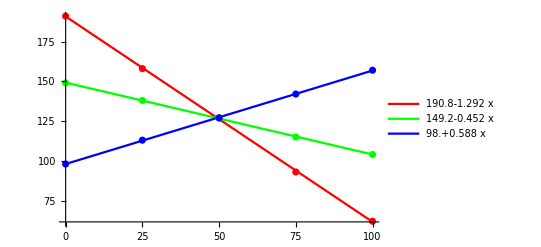

```mathematica
(*Задание 17*)
(*Построить совмещенные точечные и линейные графики для каждого цвета используя следующие функции:Show[],ListPlot[],Plot[],PlotStyle->RGBColor[*,*,*].*)
Show[Plot[ss,{x,0,100},PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue}],
ListPlot[lst,PlotLegends->"Expressions",PlotStyle->{Red,Green,Blue}]]
```

```mathematica
(*Задание 18*)
(*Проверить полученные результаты для прозрачности 20% и 80% с использованием теоретической формулы для встраивания видимого ЦВЗ:IW=pI0+(1-p)I'*)
```

```mathematica
rgb[[5]];
pl20=0.2;
pl80=0.8;
Th20=rgb[[5,All]]*pl20+(1-pl20)*(255-rgb[[5,All]])
ss/.x->20
Th80=rgb[[5,All]]*pl80+(1-pl80)*(255-rgb[[5,All]])
ss/.x->80
PercentForm[Abs[Th20-ss/.x->20]/((Th20+ss/.x->20)/2)]
PercentForm[Abs[Th80-ss/.x->80]/((Th80+ss/.x->80)/2)]
```

{166.8,141.6,109.8}

{164.96,140.16,109.76}

{88.2,113.4,145.2}

{87.44,113.04,145.04}

{1.109%,1.022%,0.03644%}

{0.8654%,0.318%,0.1103%}

```mathematica
(*Задание 19*)
(*19. Импортировать контейнер-оригинал (risO) в пакет "Mathematica".*)
```

```mathematica
risO=Import["D:\\GitHub Repos\\stud\\mag\\Sem9\\ЦТЗИ\\Lab4\\OUT\\risO.bmp"]
```

-Graphics-

```mathematica
(*Задание 20*)
(*Создать графический объект-ЦВЗ,содержащий:фамилию,имя,отчество,используя следующую конструкцию-Graphics[Text["Фамилия Имя Отчество"]].*)
cwm=Graphics[Text[Style["Кутузов Илья Геннадьевич",White,Large]]]
```

-Graphics-

```mathematica
(*Задание 21*)
(*Произвести встраивание ЦВЗ в контейнер–оригинал с помощью функции ImageCompose[контейнер оригинал,{ЦВЗ,прозрачность}].Величина прозрачности варьируется от 0 до 1,положение ЦВЗ регулируется опциями функции ImageCompose[].*)
ImageCompose[risO,{cwm,1}]
```

-Graphics-

```mathematica
(*Задание 22*)
(*Создать динамический модуль отображения ЦВЗ в виде:Manipulate[ImageCompose[контейнер оригинал,{ЦВЗ,a}],{a,0,1,0.01}].*)
Manipulate[ImageCompose[risO,{cwm,a}],{a,0,1,0.01}]
```